```mathematica
etaRho = Log[rho / (rhoMax - rho)];
```

```mathematica
etaNC = DRhoOverT*etaRho - rho;
```

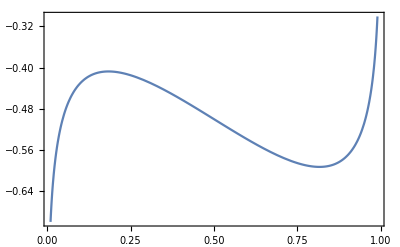

```mathematica
etaOfRhoPlt = Plot[etaNC/.{DRhoOverT->.15,rhoMax->1},{rho,0.01,.99}, Frame->{True, True, False, False}]
```

```mathematica
Export[NotebookDirectory[]<>"etaNCOfRhoVolumeFilling.pdf", etaOfRhoPlt]
```